## Flatness of a function evaluation.

### Try to figure out a way to measure the “flatness” of a function. Find the outermost root (hopefully; this concept makes the most sense for polynomials of a fixed order) and integrate its derivative squared over the middle. Lower is more flat (thus the function is poorly named).

```mathematica
flatness[f_,var_]:=Module[{},
root=var /.FindRoot[f,{var,100}][[1]];
Print[root];
(* Next, normalize the function so that its derivative is 1 at the root *)
g = f/(D[f,var]/.var->root);
Integrate[D[g,x]^2/(2*root),{x,0,root}]
]
```

### Try it out on Laguerre.

```mathematica
laguerreFlats = Table[flatness[LaguerreL[n,x],x],{n,3,10}]
```

6.28995

9.39507

12.6408

15.9829

19.3957

22.8631

26.3741

29.9207

{0.0741223,0.0344234,0.0230151,0.0174799,0.0140797,0.0117657,0.0100903,0.00882285}

### And now on polynomials:

```mathematica
polynomialFlats=Table[flatness[x^n-5,x],{n,3,10}]
```

1.70998

1.49535

1.37973

1.30766

1.2585

1.22284

1.19581

1.17462

{0.1,0.0714286,0.0555556,0.0454545,0.0384615,0.0333333,0.0294118,0.0263158}

### Stare at the results.

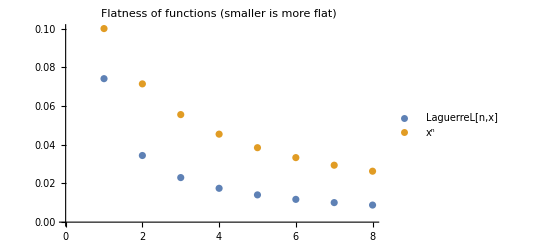

```mathematica
ListPlot[{laguerreFlats,polynomialFlats},PlotLegends->{"LaguerreL[n,x]","x^n"},PlotLabel->"Flatness of functions (smaller is more flat)"]
```

### For comparison, a function who should not be flat at all:

```mathematica
flatness[Sin[x]-0.5,x]
```

101.055

0.334762

### About a factor of 10 different.

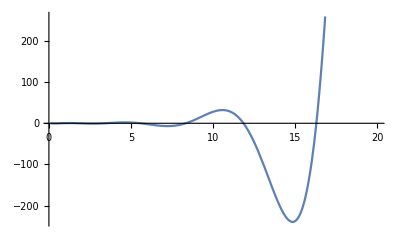

```mathematica
Plot[LaguerreL[10,x],{x,0.1,20}]
```

### Finally, a different function just for visualization:

```mathematica
normalizedLaguerre[n_]:=(
f= LaguerreL[n,x];
root=x /.FindRoot[f,{x,100}][[1]];
(* Next, normalize the function so that its derivative is 1 at the root *)
g = f/(D[f,x]/.x->root)
)
```

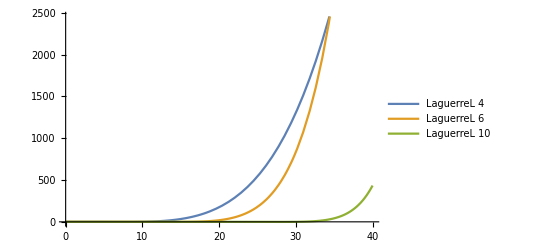

```mathematica
Plot[{Evaluate[normalizedLaguerre[4]],Evaluate[normalizedLaguerre[6]],Evaluate[normalizedLaguerre[10]]},{x,0,40},PlotLegends->{"LaguerreL 4","LaguerreL 6","LaguerreL 10"}]
```